```mathematica
(*custom styling*)
```

```mathematica
makemaze[n_,m_]:=
Module[{x=n,y=m},
x=30;y=40;edges = 2m*n-m-n;style={Background->GrayLevel[0],BaseStyle->{Directive[White,EdgeForm[],Opacity[1]]},VertexShapeFunction->(Rectangle[#1+.36,#1-.36]&),EdgeShapeFunction->(Rectangle[#1[[1]]+.36,#1[[2]]-.36]&)};
embedding=GraphEmbedding[GridGraph[{m,n}]];
g=GridGraph[{m,n},EdgeWeight->RandomReal[10,edges]];
tree=FindSpanningTree[{g,1}];
maze=Graph[tree,VertexCoordinates->embedding,style];
letsgo=HighlightGraph[maze,PathGraph[FindShortestPath[maze,1,m*n]],GraphHighlightStyle->{"Dashed"}];Show@letsgo
]
```

```mathematica
mazes=Table[Export["/home/russellfoltzsmith/Documents/art/themaze/baseimages/maze_"<>ToString[i]<>".png",Show[makemaze[40,50]]],{i,1,1000}];
```

```mathematica
Show[makemaze[200,300]]
```

$Aborted

```mathematica
Image[MorphologicalComponents[ImageResize[Import["/home/russellfoltzsmith/Documents/art/themaze/sketches/File_000.png"],500]]//Colorize]
```

-Graphics-

0

```mathematica
style2={Background->GrayLevel[0],BaseStyle->{Directive[White,EdgeForm[],Opacity[1]]},VertexShapeFunction->(Rectangle[#1+.30,#1-.30]&),EdgeShapeFunction->(Rectangle[#1[[1]]+.30,#1[[2]]-.30]&)}
```

{Background→GrayLevel[0],BaseStyle→{Directive[GrayLevel[1],EdgeForm[],Opacity[1]]},VertexShapeFunction→(Rectangle[#1+0.3,#1-0.3]&),EdgeShapeFunction→(Rectangle[#1⟦1⟧+0.3,#1⟦2⟧-0.3]&)}

```mathematica
gg2=MorphologicalGraph[ColorNegate[Image[WatershedComponents[ImageResize[Import["/home/russellfoltzsmith/Documents/art/themaze/beardither.png"],500]]]],style2]
```

-Graphics-

```mathematica
VertexCount[gg2]
```

36263

$Aborted

Part::partd: Part specification … is longer than depth of object.

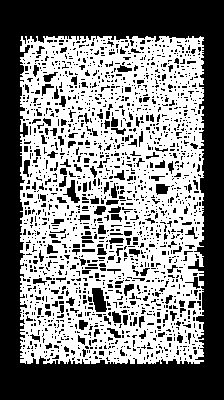
(-Graphics-)⟦1⟧

```mathematica
gg=MorphologicalGraph[ColorNegate[Image[WatershedComponents[ImageResize[Import["/home/russellfoltzsmith/Documents/art/themaze/queen.jpg"],1000]]]],style2]
```

```mathematica
HighlightGraph[gg2,PathGraph[FindShortestPath[gg2,1,36263]]]
```

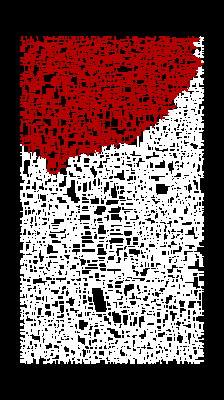

```mathematica
mazequeen=Show@HighlightGraph[gg,NeighborhoodGraph[gg,{17},50]]
```

```mathematica
ImageCompose[ConformImages[{queencomic,mazequeen}]]
```

ImageCompose::argbu: ImageCompose called with 1 argument; between 2 and 5 arguments are expected.

ImageCompose[{-Graphics-,-Graphics-}]

```mathematica
(*mosaic*)
f=FileNames["*.jpg",{"/home/russellfoltzsmith/Documents/art/themaze/baseimages"}];imgs=ConformImages[Import[#]&/@f];
m=Import["/home/russellfoltzsmith/Documents/art/themaze/clown.png"];ImageResize[m,200];
imagePool=Map[With[{i=#},{i,N@Mean[Flatten[ImageData[RemoveAlphaChannel[i]],1]]}]&,imgs];
closeMatch[c_]:=RandomChoice[Nearest[imagePool[[All,2]]->imagePool[[All,1]],c,20]]
ImageAssemble[Map[closeMatch,ImageData[m],{2}]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Nearest::near1: Symbol[]→Symbol[] is neither a list of real points nor a valid list of rules.

RandomChoice::lrwl: The items for choice Nearest[Symbol[]→Symbol[],{0.380392,0.,0.},20] should be a list or a rule weights -> choices.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Nearest::near1: Symbol[]→Symbol[] is neither a list of real points nor a valid list of rules.

RandomChoice::lrwl: The items for choice Nearest[Symbol[]→Symbol[],{0.380392,0.,0.},20] should be a list or a rule weights -> choices.

Nearest::near1: Symbol[]→Symbol[] is neither a list of real points nor a valid list of rules.

General::stop: Further output of Nearest::near1 will be suppressed during this calculation.

RandomChoice::lrwl: The items for choice Nearest[Symbol[]→Symbol[],{0.392157,0.,0.},20] should be a list or a rule weights -> choices.

General::stop: Further output of RandomChoice::lrwl will be suppressed during this calculation.

$Aborted

```mathematica
f=FileNames["*.png",{"/home/russellfoltzsmith/Documents/art/themaze/baseimages"}];imgs=ConformImages[ImageResize[Import[#],50]&/@f]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
imagePool=Map[With[{i=#},{i,N@Mean[Flatten[ImageData[RemoveAlphaChannel[i]],1]]}]&,imgs];
```

```mathematica
m=ImageResize[Import["/home/russellfoltzsmith/Documents/art/themaze/queen.jpg"],80];
```

```mathematica
closeMatch[c_]:=RandomChoice[Nearest[imagePool[[All,2]]->imagePool[[All,1]],c,20]];
```

```mathematica
assemblelist=Map[closeMatch,ImageData[m],{2}];
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,24436,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
 |  |  |  |

```mathematica
ImageCollage[Flatten@assemblelist]
```

```mathematica
(*Van Gogh style*)
img=Import["/home/russellfoltzsmith/Downloads/clown.jpg"];
im=img~ImageResize~200~ColorConvert~"Grayscale";

gof=im~GradientOrientationFilter~5;

lines=MapIndexed[{GrayLevel@RandomReal[],Line[{#2-2 {Cos[#1],Sin[#1]},#2+2 {Cos[#1],Sin[#1]}}]}&,Reverse/@Transpose@ImageData@gof,{2}];

brush=Image[Graphics[lines,PlotRange->{{1,#1},{1,#2}}&@@ImageDimensions[im],Background->GrayLevel[0.5],ImageSize->ImageDimensions[gimg]],ColorSpace->"Grayscale"];
```

```mathematica
brush
```

-Graphics-

```mathematica
tm=Image`ToneMapHDRI[img,Method->{"AdaptiveLog","Bias"->1.0}];
```

```mathematica
Export["/home/russellfoltzsmith/Documents/art/themaze/beardither.png",ColorQuantize[ImageResize[Import["/home/russellfoltzsmith/Documents/art/themaze/sketches/File_000.png"],2000],32,Dithering->False]^1.2-EdgeDetect[ImageResize[Import["/home/russellfoltzsmith/Documents/art/themaze/sketches/File_000.png"],2000]]]
```

/home/russellfoltzsmith/Documents/art/themaze/beardither.png

```mathematica
ColorToneMapping[ImageExposureCombine[{ImageResize[Import["/home/russellfoltzsmith/Documents/art/themaze/sketches/File_000.png"],2000],brush},"HDR"]]
```

```mathematica
ImageData@tm
```

ImageData::imginv: Expecting an image or graphics instead of «1».

ImageData[Image`ToneMapHDRI[-Graphics-,Method→{AdaptiveLog,Bias→1.}]]

```mathematica
throwthis=ImageData@Blur[brush,2]+ImageData@tm
```

ImageData::imginv: Expecting an image or graphics instead of ….

$Aborted[]

```mathematica
Image[0.7 (ImageData@Blur[brush,2]-0.6)+ImageData@tm]
```

ImageData::imginv: Expecting an image or graphics instead of ….

$Aborted

```mathematica
(*Vectorization in fun ways, with animation*)
```

```mathematica
(*gimg=ColorConvert[ImageResize[Import["http://i.stack.imgur.com/wtgxH.jpg"],300],"Grayscale"];*)
gimg= ColorConvert[Image[Blend[{Image[WatershedComponents[ImageResize[Import["/home/russellfoltzsmith/Documents/art/themaze/beardither.png"],2000]]],ImageEffect[ImageResize[Import["/home/russellfoltzsmith/Documents/art/themaze/beardither.png"],2000],"Comics"]}]],"CMYK"];
```

```mathematica
data=MapIndexed[Append[#2,#1]&,ImageData[gimg],{2}];
```

```mathematica
outgimg=Table[Rotate[ListDensityPlot[(MapThread[Append,{3 RandomReal[{-1,1},{Length[#],2}],ConstantArray[0,Length[#]]}]+#)&@Flatten[Transpose@data,1][[1;;-1;;15]],InterpolationOrder->0,ColorFunction->"GrayTones",BoundaryStyle->Directive[Black,Opacity[.2]],Frame->False,PlotRangePadding->0,AspectRatio->Automatic,ImageSize->300],-Pi/2],{10}];
```

ListDensityPlot::gmat: {{0.567613+Transpose[data],1.58715+Transpose[data],Transpose[data]}} is not a rectangular array larger than 2 x 2.

ListDensityPlot::gmat: {{-1.7584+Transpose[data],-2.38152+Transpose[data],Transpose[data]}} is not a rectangular array larger than 2 x 2.

ListDensityPlot::gmat: {{0.598511+Transpose[data],-2.11114+Transpose[data],Transpose[data]}} is not a rectangular array larger than 2 x 2.

General::stop: Further output of ListDensityPlot::gmat will be suppressed during this calculation.

/home/russellfoltzsmith/Documents/art/themaze/queenout.png

```mathematica
/home/russellfoltzsmith/Documents/art/themaze/sketches
```

```mathematica
Export["/home/russellfoltzsmith/Documents/art/themaze/bearrugcolor.png",gimg]
```

/home/russellfoltzsmith/Documents/art/themaze/bearrugcolor.png

```mathematica
Export["/home/russellfoltzsmith/Documents/art/themaze/test2.gif",outgimg,ConversionOptions->{"Loop"->True}]
```

ListDensityPlot::arrayerr: {«1»} must be a valid array.

ListDensityPlot::arrayerr: {{«1»}} must be a valid array.

General::stop: Further output of ListDensityPlot::arrayerr will be suppressed during this calculation.

$Aborted

```mathematica
(*colorization*)
```

```mathematica
Grid[Partition[Rotate[ListDensityPlot[(MapThread[Append,{3 RandomReal[{-1,1},{Length[#],2}],ConstantArray[0,Length[#]]}]+#)&@Flatten[Transpose@data,1][[1;;-1;;45]],InterpolationOrder->0,ColorFunction->#,BoundaryStyle->Directive[Black,Opacity[.2]],Frame->False,PlotRangePadding->0,AspectRatio->Automatic,ImageSize->300],-Pi/2]&/@{"CherryTones","CoffeeTones","DarkRainbow","DeepSeaColors","PlumColors","Rainbow","StarryNightColors","SunsetColors","ValentineTones"},3],Spacings->0]
```

```mathematica
(*animation*)
id=ParallelTable[Rotate[ListDensityPlot[(MapThread[Append,{SeedRandom[1];
200 (1-st^(1/8)) RandomReal[{-1,1},{Length[#],2}],ConstantArray[0,Length[#]]}]+#)&@Flatten[Transpose@data,1][[1;;-1;;15]],InterpolationOrder->0,ColorFunction->GrayLevel,BoundaryStyle->Opacity[.1],Frame->False,PlotRangePadding->0,AspectRatio->Automatic,ImageSize->1000],-Pi/2],{st,0.2,1,.05}];

idd=id~Join~Table[id[[-1]],{7}];

Export["/home/russellfoltzsmith/Documents/art/themaze/appear.gif",idd,ImageSize->1000,ConversionOptions->{"Loop"->True}]
```

ListDensityPlot::arrayerr: {{13.06,-13.7651,{0.,0.,0.,0.5,1.}},{27.0013,-10.8627,{0.,0.,0.,0.5,1.}},{21.1724,-15.5008,{0.,0.,0.,0.5,1.}},{47.6053,-9.21546,{0.,0.,0.,0.5,1.}},{57.0485,8.6175,{0.,0.,0.,0.5,1.}},«42»,{700.742,-13.5445,{0.,0.,0.,0.5,1.}},{707.32,-9.11046,{0.,0.,0.,0.5,1.}},{741.456,-16.5924,{0.,0.,0.,0.5,1.}},«199817»} must be a valid array.

ListDensityPlot::arrayerr: {{10.1415,-10.192,{0.,0.,0.,0.5,1.}},{24.339,-7.99197,{0.,0.,0.,0.5,1.}},{23.5506,-11.5077,{0.,0.,0.,0.5,1.}},{47.2168,-6.74336,{0.,0.,0.,0.5,1.}},{58.0047,6.7741,{0.,0.,0.,0.5,1.}},«42»,{702.015,-10.0248,{0.,0.,0.,0.5,1.}},{710.631,-6.66377,{0.,0.,0.,0.5,1.}},{740.136,-12.3351,{0.,0.,0.,0.5,1.}},«199817»} must be a valid array.

ListDensityPlot::arrayerr: {{24.1357,-27.3251,{0.,0.,0.,0.5,1.}},{37.1047,-21.7572,{0.,0.,0.,0.5,1.}},{12.1468,-30.655,{0.,0.,0.,0.5,1.}},{49.0795,-18.5972,{0.,0.,0.,0.5,1.}},{53.4195,15.6133,{0.,0.,0.,0.5,1.}},«42»,{695.913,-26.9019,{0.,0.,0.,0.5,1.}},{694.757,-18.3958,{0.,0.,0.,0.5,1.}},{746.467,-32.7489,{0.,0.,0.,0.5,1.}},«199817»} must be a valid array.

ListDensityPlot::arrayerr: {{16.6133,-18.1154,{0.,0.,0.,0.5,1.}},{30.2426,-14.3578,{0.,0.,0.,0.5,1.}},{18.2768,-20.3625,{0.,0.,0.,0.5,1.}},{48.0782,-12.2253,{0.,0.,0.,0.5,1.}},{55.8842,10.8619,{0.,0.,0.,0.5,1.}},«42»,{699.193,-17.8298,{0.,0.,0.,0.5,1.}},{703.29,-12.0893,{0.,0.,0.,0.5,1.}},{743.064,-21.7756,{0.,0.,0.,0.5,1.}},«199817»} must be a valid array.

ListDensityPlot::arrayerr: {{11.5368,-11.9002,{0.,0.,0.,0.5,1.}},{25.6118,-9.36443,{0.,0.,0.,0.5,1.}},{22.4136,-13.4168,{0.,0.,0.,0.5,1.}},{47.4025,-7.92524,{0.,0.,0.,0.5,1.}},{57.5476,7.65541,{0.,0.,0.,0.5,1.}},«42»,{701.406,-11.7075,{0.,0.,0.,0.5,1.}},{709.048,-7.8335,{0.,0.,0.,0.5,1.}},{740.767,-14.3704,{0.,0.,0.,0.5,1.}},«199817»} must be a valid array.

ListDensityPlot::arrayerr: {{8.85314,-8.61461,{0.,0.,0.,0.5,1.}},{23.1637,-6.72466,{0.,0.,0.,0.5,1.}},{24.6005,-9.74489,{0.,0.,0.,0.5,1.}},{47.0453,-5.65202,{0.,0.,0.,0.5,1.}},{58.4269,5.96031,{0.,0.,0.,0.5,1.}},«42»,{702.576,-8.47098,{0.,0.,0.,0.5,1.}},{712.092,-5.58365,{0.,0.,0.,0.5,1.}},{739.553,-10.4557,{0.,0.,0.,0.5,1.}},«199817»} must be a valid array.

ListDensityPlot::arrayerr: {{21.1991,-23.7298,{0.,0.,0.,0.5,1.}},{34.4258,-18.8687,{0.,0.,0.,0.5,1.}},{14.5398,-26.637,{0.,0.,0.,0.5,1.}},{48.6886,-16.1097,{0.,0.,0.,0.5,1.}},{54.3817,13.7584,{0.,0.,0.,0.5,1.}},«42»,{697.194,-23.3604,{0.,0.,0.,0.5,1.}},{698.088,-15.9339,{0.,0.,0.,0.5,1.}},{745.139,-28.4652,{0.,0.,0.,0.5,1.}},«199817»} must be a valid array.

ListDensityPlot::arrayerr: {{14.7392,-15.8209,{0.,0.,0.,0.5,1.}},{28.5331,-12.5144,{0.,0.,0.,0.5,1.}},{19.804,-17.7984,{0.,0.,0.,0.5,1.}},{47.8288,-10.6378,{0.,0.,0.,0.5,1.}},{56.4983,9.67815,{0.,0.,0.,0.5,1.}},«42»,{700.01,-15.5696,{0.,0.,0.,0.5,1.}},{705.416,-10.5182,{0.,0.,0.,0.5,1.}},{742.216,-19.0419,{0.,0.,0.,0.5,1.}},«199817»} must be a valid array.

ListDensityPlot::arrayerr: {{7.6555,-7.14834,{0.,0.,0.,0.5,1.}},{22.0712,-5.54661,{0.,0.,0.,0.5,1.}},{25.5765,-8.10624,{0.,0.,0.,0.5,1.}},{46.8859,-4.63755,{0.,0.,0.,0.5,1.}},{58.8193,5.20383,{0.,0.,0.,0.5,1.}},«42»,{703.098,-7.0266,{0.,0.,0.,0.5,1.}},{713.451,-4.57961,{0.,0.,0.,0.5,1.}},{739.011,-8.70861,{0.,0.,0.,0.5,1.}},«199817»} must be a valid array.

ListDensityPlot::arrayerr: {{18.7382,-20.7169,{0.,0.,0.,0.5,1.}},{32.181,-16.448,{0.,0.,0.,0.5,1.}},{16.5452,-23.2699,{0.,0.,0.,0.5,1.}},{48.3611,-14.0252,{0.,0.,0.,0.5,1.}},{55.188,12.204,{0.,0.,0.,0.5,1.}},«42»,{698.267,-20.3924,{0.,0.,0.,0.5,1.}},{700.88,-13.8707,{0.,0.,0.,0.5,1.}},{744.025,-24.8753,{0.,0.,0.,0.5,1.}},«199817»} must be a valid array.

General::stop: Further output of ListDensityPlot::arrayerr will be suppressed during this calculation.

ListDensityPlot::arrayerr: {{5.48425,-4.49008,{0.,0.,0.,0.5,1.}},{20.0906,-3.41089,{0.,0.,0.,0.5,1.}},{27.3458,-5.13548,{0.,0.,0.,0.5,1.}},{46.5969,-2.7984,{0.,0.,0.,0.5,1.}},{59.5307,3.8324,{0.,0.,0.,0.5,1.}},«42»,{704.045,-4.40806,{0.,0.,0.,0.5,1.}},{715.914,-2.75936,{0.,0.,0.,0.5,1.}},{738.029,-5.54134,{0.,0.,0.,0.5,1.}},«199817»} must be a valid array.

ListDensityPlot::arrayerr: {{3.55307,-2.12573,{0.,0.,0.,0.5,1.}},{18.3289,-1.5113,{0.,0.,0.,0.5,1.}},{28.9195,-2.49318,{0.,0.,0.,0.5,1.}},{46.3398,-1.16258,{0.,0.,0.,0.5,1.}},{60.1635,2.6126,{0.,0.,0.,0.5,1.}},«42»,{704.887,-2.07903,{0.,0.,0.,0.5,1.}},{718.104,-1.14036,{0.,0.,0.,0.5,1.}},{737.155,-2.72425,{0.,0.,0.,0.5,1.}},«199817»} must be a valid array.

ListDensityPlot::arrayerr: {{6.53592,-5.77763,{0.,0.,0.,0.5,1.}},{21.0499,-4.44535,{0.,0.,0.,0.5,1.}},{26.4888,-6.5744,{0.,0.,0.,0.5,1.}},{46.7369,-3.68921,{0.,0.,0.,0.5,1.}},{59.1861,4.49667,{0.,0.,0.,0.5,1.}},«42»,{703.586,-5.67638,{0.,0.,0.,0.5,1.}},{714.721,-3.64102,{0.,0.,0.,0.5,1.}},{738.505,-7.07544,{0.,0.,0.,0.5,1.}},«199817»} must be a valid array.

ListDensityPlot::arrayerr: {{1.81139,0.00660963,{0.,0.,0.,0.5,1.}},{16.7402,0.201881,{0.,0.,0.,0.5,1.}},{30.3388,-0.110172,{0.,0.,0.,0.5,1.}},{46.108,0.312707,{0.,0.,0.,0.5,1.}},{60.7341,1.5125,{0.,0.,0.,0.5,1.}},«42»,{705.646,0.0214504,{0.,0.,0.,0.5,1.}},{720.08,0.319771,{0.,0.,0.,0.5,1.}},{736.367,-0.183609,{0.,0.,0.,0.5,1.}},«199817»} must be a valid array.

ListDensityPlot::arrayerr: {{4.49224,-3.27555,{0.,0.,0.,0.5,1.}},{19.1857,-2.43511,{0.,0.,0.,0.5,1.}},{28.1542,-3.77818,{0.,0.,0.,0.5,1.}},{46.4648,-1.95811,{0.,0.,0.,0.5,1.}},{59.8558,3.20582,{0.,0.,0.,0.5,1.}},«42»,{704.477,-3.21168,{0.,0.,0.,0.5,1.}},{717.039,-1.92771,{0.,0.,0.,0.5,1.}},{737.58,-4.09425,{0.,0.,0.,0.5,1.}},«199817»} must be a valid array.

ListDensityPlot::arrayerr: {{2.66105,-1.03363,{0.,0.,0.,0.5,1.}},{17.5152,-0.633878,{0.,0.,0.,0.5,1.}},{29.6464,-1.2727,{0.,0.,0.,0.5,1.}},{46.2211,-0.407,{0.,0.,0.,0.5,1.}},{60.4557,2.04918,{0.,0.,0.,0.5,1.}},«42»,{705.276,-1.00325,{0.,0.,0.,0.5,1.}},{719.116,-0.392538,{0.,0.,0.,0.5,1.}},{736.752,-1.42304,{0.,0.,0.,0.5,1.}},«199817»} must be a valid array.

ListDensityPlot::arrayerr: {{1.,1.,{0.,0.,0.,0.5,1.}},{16.,1.,{0.,0.,0.,0.5,1.}},{31.,1.,{0.,0.,0.,0.5,1.}},{46.,1.,{0.,0.,0.,0.5,1.}},{61.,1.,{0.,0.,0.,0.5,1.}},{76.,1.,{0.,0.,0.,0.5,1.}},{91.,1.,{0.,0.,0.,0.5,1.}},{106.,1.,{0.,0.,0.,0.5,1.}},{121.,1.,{0.,0.,0.,0.5,1.}},«34»,{646.,1.,{0.,0.,0.,0.5,1.}},{661.,1.,{0.,0.,0.,0.5,1.}},{676.,1.,{0.,0.,0.,0.5,1.}},{691.,1.,{0.,0.,0.,0.5,1.}},{706.,1.,{0.,0.,0.,0.5,1.}},{721.,1.,{0.,0.,0.,0.5,1.}},{736.,1.,{0.,0.,0.,0.5,1.}},«199817»} must be a valid array.

ListDensityPlot::arrayerr: {{24.1357,-27.3251,{0.,0.,0.,0.5,1.}},{37.1047,-21.7572,{0.,0.,0.,0.5,1.}},{12.1468,-30.655,{0.,0.,0.,0.5,1.}},{49.0795,-18.5972,{0.,0.,0.,0.5,1.}},{53.4195,15.6133,{0.,0.,0.,0.5,1.}},«42»,{695.913,-26.9019,{0.,0.,0.,0.5,1.}},{694.757,-18.3958,{0.,0.,0.,0.5,1.}},{746.467,-32.7489,{0.,0.,0.,0.5,1.}},«199817»} must be a valid array.

ListDensityPlot::arrayerr: {{21.1991,-23.7298,{0.,0.,0.,0.5,1.}},{34.4258,-18.8687,{0.,0.,0.,0.5,1.}},{14.5398,-26.637,{0.,0.,0.,0.5,1.}},{48.6886,-16.1097,{0.,0.,0.,0.5,1.}},{54.3817,13.7584,{0.,0.,0.,0.5,1.}},«42»,{697.194,-23.3604,{0.,0.,0.,0.5,1.}},{698.088,-15.9339,{0.,0.,0.,0.5,1.}},{745.139,-28.4652,{0.,0.,0.,0.5,1.}},«199817»} must be a valid array.

ListDensityPlot::arrayerr: {{18.7382,-20.7169,{0.,0.,0.,0.5,1.}},{32.181,-16.448,{0.,0.,0.,0.5,1.}},{16.5452,-23.2699,{0.,0.,0.,0.5,1.}},{48.3611,-14.0252,{0.,0.,0.,0.5,1.}},{55.188,12.204,{0.,0.,0.,0.5,1.}},«42»,{698.267,-20.3924,{0.,0.,0.,0.5,1.}},{700.88,-13.8707,{0.,0.,0.,0.5,1.}},{744.025,-24.8753,{0.,0.,0.,0.5,1.}},«199817»} must be a valid array.

General::stop: Further output of ListDensityPlot::arrayerr will be suppressed during this calculation.

Export::convoptobs: ConversionOptions is obsolete. See the GIF format page for available options.

$Failed

```mathematica
(*Periodic Tiling*)
```

```mathematica
TranslateObject[p_,{x_,y_}]:=Map[{x,y}+#&,p,{2}]

HouseHexPolygon[s_,0]:=Polygon[s*{{1/2,-1},{3/2,0},{3/2,1},{-1/2,1},{-3/2,0},{-3/2,-1}}]
HouseHexPolygon[s_,1]:=Polygon[s*{{1,1/2},{0,3/2},{-1,3/2},{-1,-1/2},{0,-3/2},{1,-3/2}}]

HouseHexGrid[s_,imax_,jmax_]:=Block[{imod,jmod,k,m},Flatten[Table[imod=Mod[2 i,5];
jmod=Mod[2 i+3,5];
k=Range[0,Floor[(jmax-imod)/5]];
m=Range[0,Floor[(jmax-jmod)/5]];
{Table[TranslateObject[HouseHexPolygon[s,0],s*{i+1/2,j}],{j,jmod+1/2+5*m}],Table[TranslateObject[HouseHexPolygon[s,1],s*{i,j}],{j,imod+5*k}]},{i,0,imax}],2]]

HouseHexGridPerturbed[s_,h_,v_,r_]:=Block[{poly=Map[Round[#,10.^-10]&,HouseHexGrid[N[s],h,v],{2}],pts,len,rules},pts=DeleteDuplicates[Flatten[poly[[All,1]],1]];
len=Length[pts];
rules=Dispatch[Thread[pts->Range[len]]];
GraphicsComplex[pts+RandomReal[{-r,r},{len,2}],RandomSample[poly]/.rules]]

HouseHexColourCentroid[image_Image,s_,t_,opts___]:=Block[{d,dim,g,centroids,colours,rr,gg,bb,greys},d=Reverse[ImageData[image]];(*Reverse to get bottom of image on bottom*)dim=Dimensions[d];(*dim[[1]] is number of rows,dim[[2]] is number of cols*)g=HouseHexGridPerturbed[s,Floor[dim[[2]]/s-3],Floor[dim[[1]]/s-3],0];
centroids=Apply[Mean[g[[1,#]]]&,g[[2]],1];
colours=Apply[RGBColor,Extract[d,Map[Reverse,Round[centroids+s/2]]],1];
greys=colours/.RGBColor[rr_,gg_,bb_]->0.299 rr+0.587 gg+0.114 bb;
g[[2]]=Transpose[{colours,g[[2]]}][[Ordering[t*greys]]];
Graphics[{EdgeForm[{Thickness[0.0003],Black}],GraphicsComplex[g[[1]],g[[2]]]},{opts}]]
```

```mathematica
HouseHexColourCentroid[Import["http://www.eso.org/public/archives/images/screen/eso1205a.jpg"],3,1]
```

```mathematica
(*broken vectorization*)
```

```mathematica
findBestCandidate[samplePoints_,nrOfCandidates_,{w_,h_}]:=Module[{nearestFunction,candidates},nearestFunction=Nearest[samplePoints];
candidates=Transpose[{RandomInteger[{1,w},nrOfCandidates],RandomInteger[{1,h},nrOfCandidates]}];
Last@SortBy[candidates,Norm[#-First@nearestFunction@#]&]]

sample[nrOfSamplePoints_,nrOfCandidates_,{w_,h_}]:=Nest[#~Append~findBestCandidate[#,nrOfCandidates,{w,h}]&,{{RandomInteger[w],RandomInteger[h]}},nrOfSamplePoints]
```

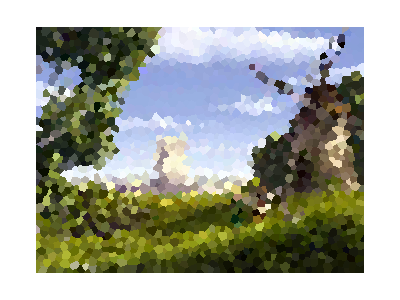

```mathematica
{w,h}=ImageDimensions[img];
pts=sample[2000,20,{w,h}];
mesh=VoronoiMesh[pts,{{0,w},{0,h}}];
coords=MeshPrimitives[mesh,0];
polys=MeshPrimitives[mesh,2];
colorList=RGBColor@@Extract[ImageData[img,DataReversed->True],Reverse@#]&/@(Mean@@@List@@@polys/.x_?NumericQ:>Round[x]);
Graphics[Transpose@{colorList,polys}]
```

```mathematica
Needs["ComputationalGeometry`"]
{w,h}=ImageDimensions[img];
{coords,polys}=BoundedDiagram[{{0,0},{0,h},{w,0},{w,h}},pts];
colorList=MapIndexed[First@#2->RGBColor@@Extract[ImageData[img,DataReversed->True],Reverse@#]&,pts];
Graphics[{First@#/.colorList,GraphicsComplex[coords,Polygon@Last@#]}&/@polys]
```

Set::shape: Lists {coords,polys} and BoundedDiagram[{{0,0},{0,768},{1024,0},{1024,768}},sample[2000,20,{1024,768}]] are not the same shape.

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[2000].

Extract::psl1: Position specification Reverse[2000] in Extract[{{{0.458824,0.443137,0.054902},«49»,«974»},{«1»},«47»,{«1»},«718»},«1»] is not applicable.

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[20].

Extract::psl1: Position specification Reverse[20] in Extract[{{{0.458824,0.443137,0.054902},«49»,«974»},{«1»},«47»,{«1»},«718»},«1»] is not applicable.

ReplaceAll::reps: {sample[1→RGBColor[{{{0.458824,0.443137,0.054902},«49»,«974»},«50»},«1»],«1»,3→«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

First::normal: Nonatomic expression expected at position 1 in First[2].

ReplaceAll::reps: {sample[1→RGBColor[{{{0.458824,0.443137,0.054902},«49»,«974»},«50»},«1»],«1»,3→«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Last::normal: Nonatomic expression expected at position 1 in Last[2].

-Graphics-